# Guy Francis Mongelli ChE 400 Prof. Alfred Clark, Jr. 12/10/2010

## 1. Introduction: THE PLATONIAN REACTOR MELT DOWN ON GLIA - 6

This notebook uses Mathematica to solve the problems encountered by the upper level cadets from Starfleet Academy.  This involves the analysis of two boundary value problems in partial differential equations.  Within these prblems we consider the diffusion of neutrons in a simplified, theoretical nuclear reactor slab of width L.  Our assumptions neglect the dependence of the differential equations of neutron distributions in both space and energy.  
The cadets must analyze a reactor operating under several different conditions.  As an engineer it is important to undersand the different operating conditions and how they affect the solution to the governing partial differential equations.  Our ability to understand the underlying scientific and mathermatical structure of the problem will place limitations on our ability to operate simmilar reactors in the future and to prevent the horrific accident that occured in the Glia system to happen again. The reactor is a constant size rectangular cuboid, with 5 out of the six faces contrained to zero neutron concentration.  The neutron concentration will be designated represented as N(x,t).  The sixth face obtains a boundary condition specified by a novel device, the neutorotator.  With the neutorotator off, the boundary condition is the same as the other faces (N(L,t)=0).  With the neutorotator on, there is a flux at legnth L, that is dependent upon the operating perameter β' (which has been redefined from the provious Starfleet reports as simply β.  Since β already appeared as part of another operating perameter in their text (γ), it makes sense to redefine it to avoid confusion).  

It is the goal of this report to elucidate:
(1) Full and correct solution forms of the partial differential equations, designated as N(x,t), with the neutorotator off and on
                (a) What affects the criticality condition and how we create critical systems?
(2) Reevaluate how the neutorotator affects the solution when turned on (for specific values of β')
(3) The cause of the reactor melt-down.  And also, to suggest the approriate operating conditions (γ) to obtain a stable reaction under the melt-down β' conditions.
(4) The error in the extrapolation of a trend of γ dependeng on β'.

Here are stated the important numberical constants determined via tricorder for the reactor in question:
slab thickness L = 1.2 m
neutron diffusivity D = 1.4 x 10 - 3 m2/s
neutorator parameter β = 0.0, 0.5, and 1.6 m - 1
achievable range of production coefficient:  0 ≤ γ ≤ 0.05 s - 1

## 2. Neutorotator Off

As in other problems of this sort, we must first find the eigenfunctions that satisfy the differential equation.  First we list the differential equation:

N = N(x, t), with
(∂N)/(∂t)= D(∂^2 N)/(∂x^2)+ γ N, for 0 < x < L and t > 0,
and with N(0, t) = 0 and N(L, t) = 0 (neutorator turned off).

This problem was solved many times in the course.  It has a solution that is oscillartory in x, and the boundary conditions at the endpoints dicatate that the eigenfunctions must be sine functions.  Thus, the solution is of the form:

N_Off(x,t)=∑_(n=1)^∞ c_n(t) Sin(√λx)
Substitution of this function into the boundary condition at x=L dictates that λ=(n^2 π^2)/L^2.  The cosine eigenfunctions are excluded by the boundary condition at x=0.
Subsitution of this relation into the governing differential equation will yield a relationship between three Fourier Sine Series.  These series are in the same eigenfunctions and balancing coefficients yields a differential equation of c_n(t).  This is that differential equation:

(dc_n(t))/dt =((-Dn^2 π^2)/L^2+γ)  c_n(t)

```mathematica
This equation will have the solution:

Subscript[c, n](t)=Subscript[c, n](0)  ⅇ^(((-Dn^2 π^2)/L^2+γ)t)
```

0

```mathematica
Therefore the solution can be expressed:

Subscript[N, Off](x,t)=∑_(n=1)^∞ c(0)  ⅇ^(((-Dn^2 π^2)/L^2+γ)t)Sin(√((n^2 π^2)/L^2)x)
```

```mathematica
To determine that this solution set is complete, we consider the case that λ could be zero and determine the associated eigenfunctions of this case.  When separation of variables is applied lambda equals zero does indicate an acceltable constant (with respect to space and time) solution for N(x,t).  However, the boundary condition forces this constant to zero.  Lambda less than zero would give hyperbolic functions in the spatial eigenfunctions.  The x=0 condition knocks out a possible Cosh component and the x=L condition knocks out the Sinh component since the Sinh function has no positive zeros. Checking for the eigenfunctions associated with lambda lass than or equal to zero will be imperative in examining the case for when the neutorotator is on.
```

```mathematica
The spatial eigenfunctions have no affect on the critical state of the reactor.  As is commonly known, the range of the sine function is from -1 to 1.  Therefore, the criticality of the reactor is determined by the temporal eigenfunctions.  As n increases, so does the value of lamba. It is important that there be one term of this series that does not decay exponentially with time, such that the neutron concentration is sustained for all time without external excitations.  This is the critical state of the reactor.  Subcritical states have exponential decay in all of the modes present in the system and supercritical states have exponential growth of at least one of the spatial modes.  Therefore we should like to create a solution where the neutron concentration is stable.  We do this through careful selection of the gamma perameter.  We can create a stable solution by forcing gamma to be:  γ=D*Subscript[λ, min].  This will all of the modes to decay with time, except for the first one.  For larger times, a one term approximation may be used.
```

```mathematica
L = 1.2 (* m *); 
 d = 1.4 * 10^-3 (* m2/s *);
```

```mathematica
Since the symbol D is protected as part of the differential operator, I use a lowercase 'd' to specify the numerical value of the diffusion coefficient in my mathematica code.
```

```mathematica
Lambda[n_]:=(n^2 π^2)/L^2;
```

```mathematica
This following is the operater-enforced gamma value for the case with the neutorotator off to ensure stability.
```

```mathematica
γ0=d*Lambda[1]
```

0.00959545

```mathematica
This is good because it is within the range of articulated acheiveable gamma values.
```

```mathematica
Subscript[N, Off][x_,t_,k_]:=∑_(n=1)^k c[0]*Exp[((d n^2 π^2)/L^2-γ0)t]*Sin[(n π)/L x]
```

## 3. Neutorotator On: What's different?

N = N(x, t), with
(∂N)/(∂t)= D(∂^2 N)/(∂x^2)+ γ N, for 0 < x < L and t > 0,
and with N (0, t) = 0, and
(∂N)/(∂x)(L, t) = β N (L, t) (neutorator turned on).

Quote from the Report: ME201/MTH281/ME400/CHE400 STARDATE 9966.2 PAGE 7
The parameter β, which is completely unrelated to the β we used in
the academy for non-productive capture [again, this has been restated in this document as β'], 
is adjustable to some extent. As the reactor log shows,
the Platonians tried only three different values of β before the melt down. They made many runs
with β = 0 and many runs with β = 0.5 m-1. In both cases, they calculated the critical values of γ,
which agreed very well with the actual values used to run the reactor at critical. The final entry
in the log is a brief statement of their plan to make a run with β = 1.6 m-1. They also mention the
puzzling fact that the calculated critical value of γ for this value of β is larger than the value for β
= 0.5 m-1, contrary to their expectations. They thought that since the critical γ dropped when β
increased from 0 to 0.5 m-1, there would be a further drop when β increased from 0.5 to 1.6 m-1.”

This system is different because it's boundary condition is altered.  In the first problem, the eigenvalues were determined by observing all of the lambda values for which the sine function can generate a zero value at x=L (the x=0 boundary condition already being satisfied by the nature of the sine function).  
We must consider all three cases of lambda and the associated solutions.  Any non-trivial solutions must be included in the B ranges over which they are valid.  
In this case the boundary condition at x=0 is satisfied by the nature of the sine function once again.  The boundary condition at x=L is simmilar to that considered by Newton's law of cooling, where instead of heat leaving a wall, we have neutrons diffusing into the bulk of our reactor.  It is speculated that the solution will involve observing lambda as the points at which the tangent function crosses a constant function (as was done for the case of Newton's Law of Cooling).

The follwing information will be helpful in confirming that our theoretical reactor is running simmilarly as the one the people of Glia-6 used.

From: ME201/MTH281/ME400/CHE400 STARDATE 9966.2 PAGE 8
At the end, he emphasizes the puzzling result that the critical value of γ for β
= 0.5 m-1 (namely 0.00108 s-1 ) is smaller than the critical value for β = 1.6 m-1.


The advantage of the neutorotator is that it allows the reactor to become critical at lower fuel density (or productive volumetric generation rates,  which translates to less external excitation necessary (generating the initial neutron concentration in the fuel source).

```mathematica
For the Neutorotator on, there are three cases to consider :
  (1) Lambda is less than zero
  (2) Lambda equals zero
  (3) Lambda is greater than zero
  
  I will examine the eigenfunctions associated with each case and check for any constraints placed upon β' that the reactor can operate at.   Then search for the appropriate method to determine the smallest eigenvalue.
```

```mathematica
(1) Lambda is greater than zero :
dG/dt=GD(γ/D-λ)
(d^2 F)/dx^2=-λ*F

These equations have solutions with spatial eigenfunctions of the form:
F(x)=A*Sin(√λx)+B*Cos(√λx), where B is zero from the x=0 boundary condition.
The x=L boundary condition tells that √λ=β' Tan(√λL).  There are an infinite number of lambda values that solve this system for a given value of β'.
The following graph illustrates this:
```

```mathematica
B=.5;
d=1.4*10^-3;l=1.2;
```

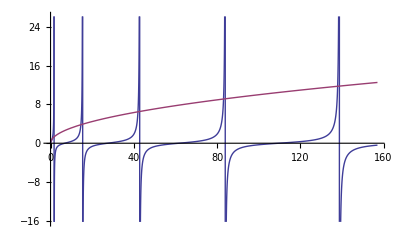

```mathematica
Plot[{B*Tan[√lambda l],√lambda},{lambda,0,50π}]
```

```mathematica
Here are the first several eigenvalues for the Sine function solution:
```

```mathematica
FindRoot[B Tan[√lambda l]==√lambda,{lambda,12}]
```

{lambda→14.5809}

```mathematica
FindRoot[B Tan[√lambda l]==√lambda,{lambda,35}]
```

{lambda→42.001}

```mathematica
FindRoot[B Tan[√lambda l]==√lambda,{lambda,80}]
```

{lambda→83.1256}

```mathematica
FindRoot[B Tan[√lambda l]==√lambda,{lambda,130}]
```

{lambda→137.957}

```mathematica
The temporal eigenfunctions will have the form :
G(t)=ⅇ^(γ-λD)
These solutions will be valid for all β'.
```

```mathematica
(2) Lambda is equal to zero :
(d^2 F)/dx^2=0
dG/dt=GD(γ/D)
```

```mathematica
The spatial eigenfunctions are:
F(x)=Ax+B.  The x=0 condition tells that B is zero.  The x=L conditions says that unless β' is exactly equal to 1/L, A will be zero and this mode will be trivial.
The temporal eigenfunctions are:
G(t)=ⅇ^(γ)


(3) Lambda is less than zero :
dG/dt=GD(γ/D+λ)
(d^2 F)/dx^2+λ*F=0

For this case we let α=-λ,
The spatial eigencuntions are:
A*Sinh(√αx)+B*Cosh(√αx)\
The x=0 condition gives that B=0 and the x=L condition tells that √α=β'*Tanh(√α L)
There is only one eigenvalue here, since the Tanh function is exponential and not hyperbolic in nature.  It can be solved for again by plotting and inserting estimated numerical values into the Findroot command.
```

```mathematica
B=1.6;
```

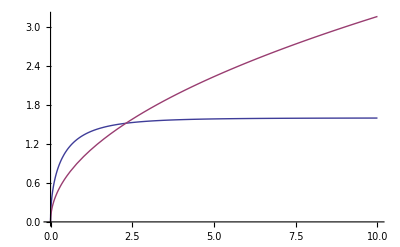

```mathematica
Plot[{B *Tanh[√alpha l],√alpha},{alpha,0,10}]
```

```mathematica
FindRoot[B Tanh[√alpha l]==√alpha,{alpha,2}]
```

{alpha→2.30581}

```mathematica
Alpha=2.30581;
```

```mathematica
There are no solutions for this relation unless β' > 1/L.  This is because of the numerical nature of the spatial eigenfunctions.  This is seen below:
```

```mathematica
B=1/l;
```

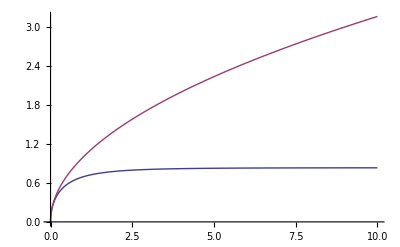

```mathematica
Plot[{B *Tanh[√alpha l],√alpha},{alpha,0,10}]
```

```mathematica
Therefore, solutons to the differential equation can be constructed for different values of β'.  The solutions are as follows:
(A) for B<1/L: (β'=0 and .5 work within this solution)
N(x,t)=∑_(n=1)^∞ Exp[(γ-Subscript[λ, n] D)t]*Sin(√Subscript[λ, n]x)
(B) for β'=1/L:
N(x,t)=x*Exp[γt]+∑_(n=1)^∞ Exp[γ-Subscript[λ, n] D]*Sin(√Subscript[λ, n]x)
(C) for β'≥1/L: (β'=1.6 operates within this solution)
N(x,t)=Exp[(γ+α)t]Sinh(√α x)+∑_(n=1)^∞ Exp[γ-Subscript[λ, n] D]*Sin(√Subscript[λ, n]x)
In cases B and C, and linear combination of the infinite sine series and the special mode are acceptable in practice and can be solved for be assuming specific neutron concentrations at two points in the slab reactor.  For simplicity, when estimating reactor meltdown when the Platonians run the reactor in the (C) solution, I will assume that the constant multaplicatives are both 1.
To run the reactor safetly in case (1), gamma must be equal to the D multiplied by the first eigenvalue such that one mode will survive with respect to time.  The higher modes will decay with time.
For case B, γ=0 is the only case that will allow the reactor to run safetly (neutron concentration doesn't take off to infinity).  This will casue the infinite series to decay with time.
For case C, Gamma must be chosen such that only one or more modes are stable and all of the other modes decay with time.  If the minimum lambda value and alpha value of not equivalent, the maximum of the two will determine lambda.

Now that correct solutions have been explored for the system, we must consider the information from the Platonians and see if they missed something that would cause the reactor to blow up.  

Let's look at first eigenvalue of the system for β'=0.
```

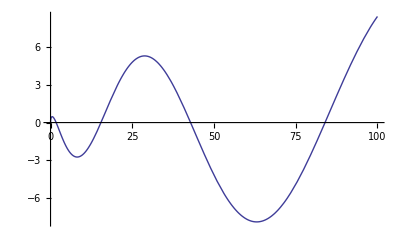

```mathematica
Plot[√λ Cos[√λ l]==0,{λ,0,100}]
```

```mathematica
FindRoot[√λ Cos[√λ l]==0,{λ,5}]
```

{λ→1.71347}

```mathematica
Gammaforbetazero=d*1.71347
```

0.00239886

```mathematica
This is also within the range of articulated possible gamma ranges.
```

```mathematica
Next, let' s examine the first eigenvalue of the system for β' = .5.
```

```mathematica
β'=.5;
```

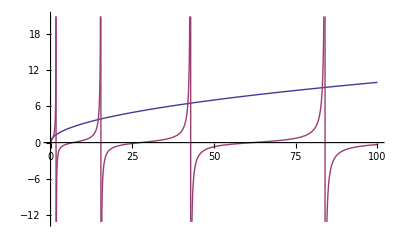

```mathematica
Plot[{√λ,β'*Tan[√λ l]},{λ,0,100}]
```

```mathematica
FindRoot[√λ==β'*Tan[√λ l],{λ,1}]
```

{λ→0.769705}

```mathematica
Gammaforbetahalf=d*.769705
```

0.00107759

```mathematica
Then above gamma value is what the Platonian' s specified, so I know they must be working with this system of equations.  Let's observe an approximated gamma for β'=1.6.
```

```mathematica
β'=1.6;
```

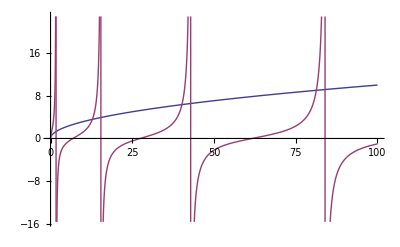

```mathematica
Plot[{√λ,β'*Tan[√λ l]},{λ,0,100}]
```

```mathematica
FindRoot[√λ==β'*Tan[√λ l],{λ,3}]
```

{λ→12.7909}

```mathematica
GammaTheoreticalforBetalarge=d*12.7909
```

0.0179073

```mathematica
The next step is to plug in alpha for this beta value and substitute this gamma into the solution for case (C).  The first term in the infinite series of case (C) will remain stable with respect to time and the higher terms of the infinite series will decay with respect to time.  However let us calculate the numerical power of the exponential in the Sinh term.
```

```mathematica
Powerofe=GammaTheoreticalforBetalarge+Alpha*d
```

0.0211354

```mathematica
This special mode will be multiplied by an exponential that is increasing with respect to time.  It is sure to cause the reactor to melt-down (Supercritical condition) and must not have been considered.  Since alpha is larger than the minimum lambda value, gamma actually should be set to alpha multiplied by D to allow the reactor to run safetly.  Now, to determine the time to meltdown.
```

```mathematica
CriticalGammaforBetaLarge=d*Alpha
```

0.00322813

```mathematica
This is also within the range of acheiveable gamma values.
```

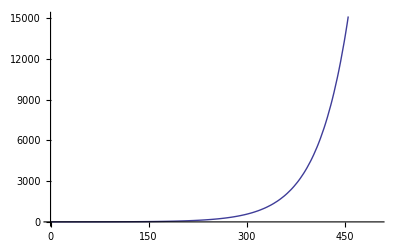

```mathematica
Plot[Exp[Powerofe*t],{t,0,500}]
```

```mathematica
N[400/60,4]
```

6.667

```mathematica
It would take approxamately six minutes for the neutron concentration to take off, at which time an explosion would occur once a specific amount of energy released is generated.
```

```mathematica
Other thoughts on the project:
```